# Assignment 1: Problem solving

Solution of Problem 3.1 (polynomial equation):

```mathematica
"function declartion"
f[x_]:=x^5-2 x^4-19/4 x^3+31/4 x^2+11/2 x-15/2;
```

```mathematica
Solve[f[x]==0,x]
```

{{x→-3/2},{x→1},{x→5/2},{x→-√2},{x→√2}}

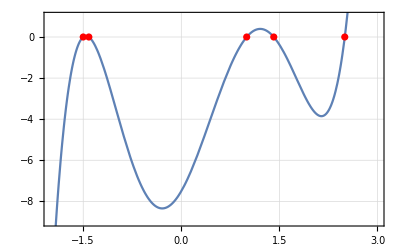

```mathematica
roots=ListPlot[{{-3/2,0},{1,0},{5/2,0},{-Sqrt[2],0},{Sqrt[2],0}},PlotStyle-> Red,PlotStyle->PointSize[0.02]];
Show[Plot[f[x],{x,-2,3}],roots,PlotRange->{{-2,3},{-9,1}} ,Frame->True,GridLines->Automatic]
```

Solution of Problem 3.2 (Equation with absolute amount):

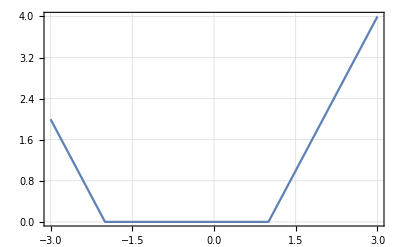

```mathematica
g[x_]:=Abs[x-1]+Abs[x+2]-3;
Plot[g[x],{x,-3,3},Frame->True,GridLines->Automatic]
```

```mathematica
"we use redcuse insteed of solve, Solve cant find values of reigon ,"
Reduce[g[x]==0,x,Integers]
```

x==-2||x==-1||x==0||x==1

Solution of Problem 3.3 (Binomial equation):

```mathematica
"Nsolve is to find  the decimal(,), ComplexExpand change it to decimal "
```

```mathematica
ComplexRoots=ComplexExpand[NSolve[z^7==1-I,z]];
z/.ComplexRoots
```

{-0.991792-0.347043 ⅈ,-0.889701+0.559036 ⅈ,-0.347043-0.991792 ⅈ,-0.117647+1.04415 ⅈ,0.559036-0.889701 ⅈ,0.742997+0.742997 ⅈ,1.04415-0.117647 ⅈ}

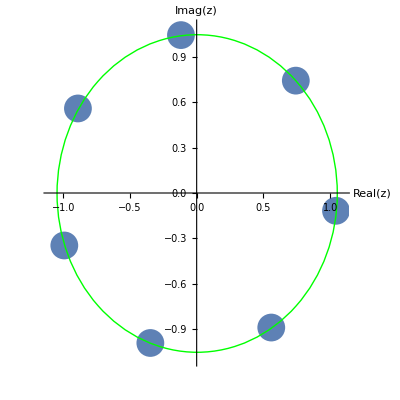

```mathematica
""
ComplexPlot=ListPlot[{Re[z],Im[z]}/.ComplexRoots,PlotRange->{{ -1.1,1.1},{-1.1,1.1}},AxesLabel->{"Real(z)","Imag(z)"}, AspectRatio->1,PlotStyle->PointSize[0.05]];
Show[ComplexPlot,Graphics[{Green,Circle[{0,0},1.05]}]]
```

Solution of Problem 3.4 (Achilles and the turtle):

// suppose that speed of Achilles is 1 m/s , then  turtles speed is 0.1 m/s 
// Distance=speed * Time

{{t→88.8889}}

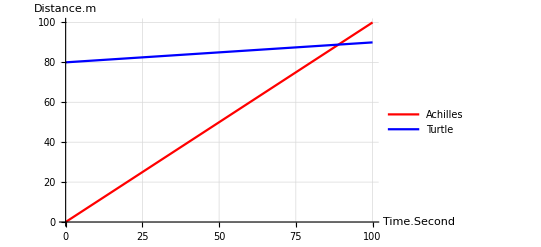

```mathematica
DistA[t_]:=t
DistT[t_]:=80+0.1t
NSolve[DistA[t]==DistT[t]]
Plot[{DistA[t],DistT[t]},{t,0,100},GridLines->Automatic,PlotStyle->{Red,Blue},AxesLabel->{Time.Second,Distance.m},PlotLegends->{"Achilles","Turtle"}]
```